Do Figure 3b using the Barbosa expression, the Liemohn and Khazanov [1998]–derived expression, and my own NIntegrate thing

## Set up functions

### Helpers

```mathematica
preFactor = 2.680594*^-08;
```

```mathematica
vbth[deltaPhi_,T_]:=√(deltaPhi/T);
```

### Liemohn and Khazanov Maxwellian and kappa funcs (LKMwellDensFac and LKKappaDensFac)

```mathematica
dir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/journals/";
SetDirectory[dir];
<<Liemohn_and_Khazanov__mapped_Maxwellian_density.wl
```

### Barbosa Maxwellian and kappa funcs (BarbosawellDensFac and BarbosaKappaDensFac)

```mathematica
dir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/journals/";
SetDirectory[dir];
<<Barbosa_funcs.wl
```

#### Some plots of the Barbosa Funcs

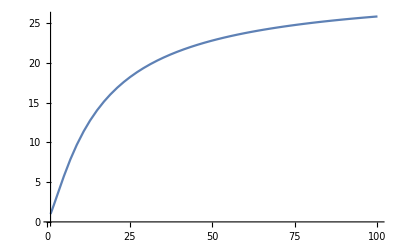

```mathematica
Plot[BarbosaKappaDensFac[941/110,RB,3],{RB,1,100}]
```

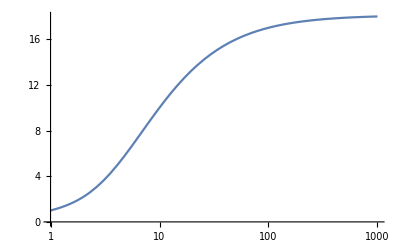

```mathematica
LogLinearPlot[BarbosaMwellDensFac[941/110,RB],{RB,1,1000}]
```

### My own ‘nilla

```mathematica
MaxwellArbPotCylUnitStep[rho_,phi_,vbth_,alpha_]:=2/(√π)Exp[-(rho^2-2 vbth(rho^2(1-alpha (Sin[phi])^2)-vbth^2)^(1/2))]UnitStep[rho^2(1-alpha(Sin[phi])^2)-vbth^2];
```

```mathematica
KappaArbPotCylUnitStep[rho_,phi_,vbth_,alpha_,kappa_]:=2/(√π(1-3/(2kappa))^(3/2))Gamma[kappa+1]/(kappa^(3/2)Gamma[kappa-1/2])(1+(rho^2-2 vbth(rho^2(1-alpha (Sin[phi])^2)-vbth^2)^(1/2))/(kappa-3/2))^(-(kappa+1))UnitStep[rho^2(1-alpha(Sin[phi])^2)-vbth^2];
```

```mathematica
SpenceMaxwellDensFac[phiBar_,RB_]:=NIntegrate[rho^2 Sin[phi] MaxwellArbPotCylUnitStep[rho,phi,√phiBar,1/RB],{rho,0,15},{phi,0,π/2}]
SpenceKappaDensFac[phiBar_,RB_,kappa_]:=NIntegrate[rho^2 Sin[phi] KappaArbPotCylUnitStep[rho,phi,√phiBar,1/RB,kappa],{rho,0,15},{phi,0,π/2}]
```

## Define functions for mapping density back to FAST

```mathematica
funkerMaxwell[densFac_,Tm_,Kmeas_]:=Kmeas/preFactor * √Tm *densFac;
```

```mathematica
funkerKappa[densFac_,Tm_,Kmeas_,κ_]:=Kmeas/preFactor * √Tm *densFac*((κ-3/2)^(1/2)Gamma[κ-1/2])/Gamma[κ];
```

### Condiciones

```mathematica
(*for using characteristic energy*)
(*Ep = 1075;*)
(*measCond = 1.40*^-9;*)
```

```mathematica
dPhi = 941;
measCond = 9.81*^-10;
```

```mathematica
minDens=1.73;
maxDens=2.07;
minT=73.14;
maxT= 153.68;
```

## Plot options

```mathematica
kappas={155/100,16/10,175/100,201/100,245/100,401/100,10};
```

```mathematica
tick = 0.002;
```

```mathematica
grayLev1=0.4;
grayLev2=0.6;
```

```mathematica
fontSize=19;
xScaled = 0.94;
```

```mathematica
styles={Directive[Dashing[{0,Small}],GrayLevel[grayLev2],Thickness[tick]],Directive[Dashing[{0,Small}],GrayLevel[grayLev2],Thickness[tick]],Directive[Dashing[{0,Small}],GrayLevel[grayLev2],Thickness[tick]],Directive[Dashing[{0,Small}],GrayLevel[grayLev2],Thickness[tick]],Directive[Dashing[{Small}],GrayLevel[grayLev1],Thickness[tick]],Directive[Dashing[{Large,Large}],GrayLevel[grayLev2],Thickness[tick]],Directive[Dashing[{Large,Large}],GrayLevel[grayLev2],Thickness[tick]],Directive[Black,Thickness[tick]]};
```

```mathematica
placeList={Below,Below,Below,Below,Below,Below,Below,Below,Below};
```

```mathematica
nDigs={3,3,3,3,3,3,3,3,3};
```

```mathematica
kapStrVals=Table[NumberForm[kappas[[k]],nDigs[[k]]],{k,1,8}];
```

Part::partw: Part 8 of {31/20,8/5,7/4,201/100,49/20,401/100,10} does not exist.

```mathematica
kapStrVals[[5]] = StringForm["κ_t (≃ 2.45)"];
```

```mathematica
kappaLabels=Table[StringForm["κ = `1`",kapStrVals[[k]]],{k,1,8}]
```

{κ = 31/20,κ = 8/5,κ = 7/4,κ = 201/100,κ = κ_t (≃ 2.45),κ = 401/100,κ = 10,κ = {31/20,8/5,7/4,201/100,49/20,401/100,10}⟦8⟧}

```mathematica
kappaLabels[[8]]=StringForm[" "];
```

## PLOHT

### Dahone

```mathematica
plotRange={{1,999},{0,10}};
RB=20;
```

```mathematica
Show[Plot[{funkerMaxwell[BarbosaMwellDensFac[dPhi/Tm,RB],Tm,measCond],funkerMaxwell[LKMwellDensFac[dPhi/Tm,RB],Tm,measCond],funkerMaxwell[SpenceMaxwellDensFac[dPhi/Tm,RB],Tm,measCond]},{Tm,1,1000},PlotRange->plotRange,LabelStyle->(FontSize->19),Frame->True,FrameLabel->{StringForm["T_m (eV)"],StringForm["n_FAST (cm^-3)"]},FrameStyle->Directive[Black,19],ImageSize->900,Epilog->{Text[Style[StringForm["R_B = `1`",RB],20],Scaled[{0.5,0.95}],{0,1}]},PlotLegends->{"Barbosa Maxwellian","L&K Maxwellian"}],ListLinePlot[{{{0,minDens},{1000,minDens}},{{0,maxDens},{1000,maxDens}},{{minT,0},{maxT,0}},{{minT,10},{maxT,10}}},Filling->{{1->{2}},{3->{4}}},PlotStyle->Directive[Gray,Thickness[0.0001]]]]
```

$Aborted

### No labels, handle manually

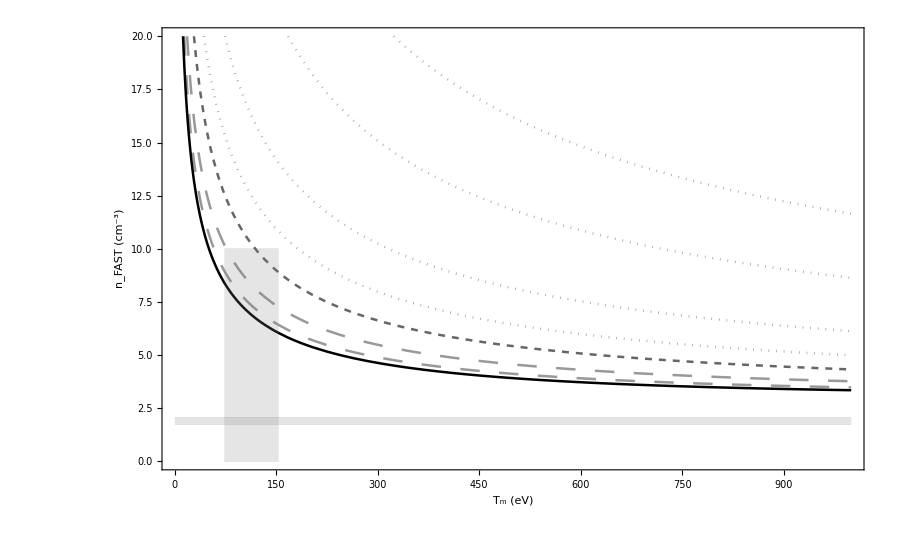

```mathematica
Show[Table[Plot[funker[Ep,Tm,kappas[[k]],measCond],{Tm,1,1000},PlotStyle->styles[[k]],PlotLegends->LineLegend[Automatic],PlotRange->{{1,999},{0,20}},PlotRangeClipping->True,LabelStyle->(FontSize->19),Frame->True,FrameLabel->{StringForm["T_m (eV)"],StringForm["n_FAST (cm^-3)"]},FrameStyle->Directive[Black,19],ImageSize->900],{k,{1,2,3,4,5,6,7,8}}],ListLinePlot[{{{0,minDens},{1000,minDens}},{{0,maxDens},{1000,maxDens}},{{minT,0},{maxT,0}},{{minT,10},{maxT,10}}},Filling->{{1->{2}},{3->{4}}},PlotStyle->Directive[Gray,Thickness[0.0001]]]]
```

## Just Maxwellian (resized)

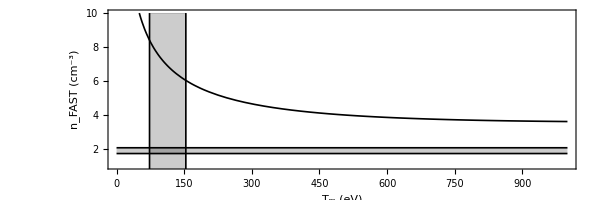

```mathematica
Show[Plot[funkerBarb[Ep,Tm,measCond],{Tm,1,1000},PlotStyle->styles[[8]],PlotLegends->LineLegend[Automatic],PlotRange->{{1,999},{1,10}},PlotRangeClipping->True,LabelStyle->(FontSize->19),Frame->True,FrameLabel->{StringForm["T_m (eV)"],StringForm["n_FAST (cm^-3)"]},FrameStyle->Directive[Black,19],ImageSize->{600,300},AspectRatio->1/3],ListLinePlot[{{{0,minDens},{1000,minDens}},{{0,maxDens},{1000,maxDens}},{{minT,0},{maxT,0}},{{minT,10},{maxT,10}},{{minT,0},{minT,10}},{{maxT,0},{maxT,10}}},Filling->{{1->{2}},{3->{4}}},PlotStyle->{Directive[Black,Thickness[0.002]],Directive[Black,Thickness[0.002]],Directive[Black,Thickness[0.0001]],Directive[Black,Thickness[0.0001]],Directive[Black,Thickness[0.002]],Directive[Black,Thickness[0.002]]}]]
```

## Maxwellian, with suggestive kappa lines

```mathematica
fakeKappa={1.53,1.6};
```

```mathematica
fakeStyles={Directive[Dashing[{0,Small}],GrayLevel[grayLev2],Thickness[tick]],Directive[Dashing[{0,Small}],GrayLevel[grayLev2],Thickness[tick]],Directive[Dashing[{0,Small}],GrayLevel[grayLev2],Thickness[tick]]};
```

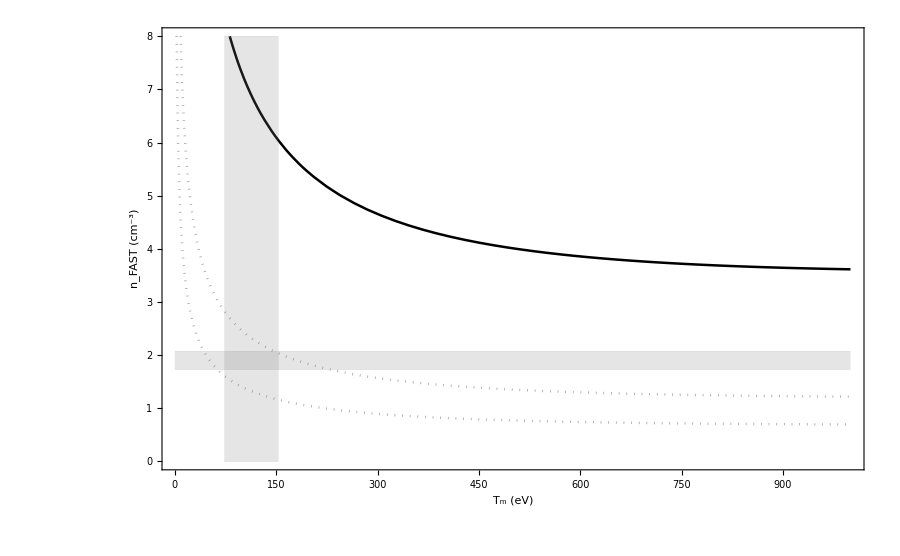

```mathematica
Show[Plot[funkerBarb[Ep,Tm,measCond],{Tm,1,1000},PlotStyle->styles[[8]],PlotLegends->LineLegend[Automatic],PlotRange->{{1,1000},{0,8}},PlotRangeClipping->True,LabelStyle->(FontSize->19),Frame->True,FrameLabel->{StringForm["T_m (eV)"],StringForm["n_FAST (cm^-3)"]},FrameStyle->Directive[Black,19],ImageSize->900],Table[Plot[funkerFake[Ep,Tm,fakeKappa[[k]],measCond],{Tm,1,1000},PlotStyle->fakeStyles[[k]],PlotLegends->LineLegend[Automatic],PlotRange->{{1,1000},{0,8}},PlotRangeClipping->True,LabelStyle->(FontSize->19),Frame->True,FrameLabel->{StringForm["T_m (eV)"],StringForm["n_FAST (cm^-3)"]},FrameStyle->Directive[Black,19],ImageSize->900],{k,{1,2}}],ListLinePlot[{{{0,minDens},{1000,minDens}},{{0,maxDens},{1000,maxDens}},{{minT,0},{maxT,0}},{{minT,8},{maxT,8}}},Filling->{{1->{2}},{3->{4}}},PlotStyle->Directive[Gray,Thickness[0.0001]]]]
```

## Maxwellian, scaled to magnetosphere properly (not bogus Barbosa density)

```mathematica
fakeKappa={1.53,1.6};
```

```mathematica
fakeStyles={Directive[Dashing[{0,Small}],GrayLevel[grayLev2],Thickness[tick]],Directive[Dashing[{0,Small}],GrayLevel[grayLev2],Thickness[tick]],Directive[Dashing[{0,Small}],GrayLevel[grayLev2],Thickness[tick]]};
```

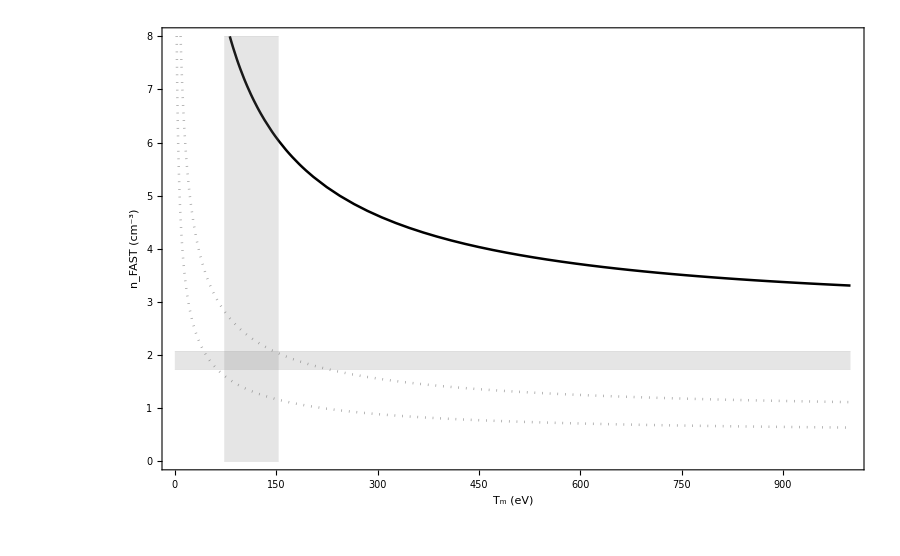

```mathematica
Show[Plot[funkerBarb2[Ep,Tm,measCond],{Tm,1,1000},PlotStyle->styles[[8]],PlotLegends->LineLegend[Automatic],PlotRange->{{1,1000},{0,8}},PlotRangeClipping->True,LabelStyle->(FontSize->19),Frame->True,FrameLabel->{StringForm["T_m (eV)"],StringForm["n_FAST (cm^-3)"]},FrameStyle->Directive[Black,19],ImageSize->900],Table[Plot[funkerFake2[Ep,Tm,fakeKappa[[k]],measCond],{Tm,1,1000},PlotStyle->fakeStyles[[k]],PlotLegends->LineLegend[Automatic],PlotRange->{{1,1000},{0,8}},PlotRangeClipping->True,LabelStyle->(FontSize->19),Frame->True,FrameLabel->{StringForm["T_m (eV)"],StringForm["n_FAST (cm^-3)"]},FrameStyle->Directive[Black,19],ImageSize->900],{k,{1,2}}],ListLinePlot[{{{0,minDens},{1000,minDens}},{{0,maxDens},{1000,maxDens}},{{minT,0},{maxT,0}},{{minT,8},{maxT,8}}},Filling->{{1->{2}},{3->{4}}},PlotStyle->Directive[Gray,Thickness[0.0001]]]]
```